## Some formulae

```mathematica
CalculateInOutFormulaMany[g_,sets_List, prefix_String:"A", verbose_:False]:=Block[{
currentEdge, 
edges, 
pos,
isInOut, gContract, gRemove, gIn, gOut, result, resIn, resOut, resContract, resRemove, repVertex, in, out,inVertex,outVertex,
 contractSets},
If[verbose,Print[{"Task ","g",Graph[g,VertexLabels->"Name"],"sets",sets,"prefix", prefix , "node count", VertexCount[g]}]];
If[VertexCount[g]==0,
Print["VertexCount is zero",g,sets,prefix];
Return[1]
];
(* if there is no set, we have a problem *)
If[Length[sets]==0,
Print["No more sets"];
Interrupt[];
];
(* if there is only one set, we are done *)
If[Length[sets]==1,
result=FindFullFormulaWithPrefix[g,prefix];
Return[result];
];

(* there is more than 1 set : we define in to be the first set, out to be thejoin of the rest *)
in=First[sets];
out=Flatten[Rest[sets]];

(* the whole goal is to remove the  in *)
(* as long as there is an edge between in and out we remove and contract it and recurse *)
edges=EdgeList[g];
For[pos=1,pos <=Length[edges],pos++,
(* make sure currentEdge is of the form {in, out} *)
currentEdge=edges[[pos]];
isInOut=MemberQ[in,currentEdge[[1]]]&&MemberQ[out,currentEdge[[2]]];
If[!isInOut,
isInOut=MemberQ[in,currentEdge[[2]]]&&MemberQ[out,currentEdge[[1]]];
currentEdge=UndirectedEdge[currentEdge[[2]],currentEdge[[1]]]
];
If[isInOut && (!MemberQ[in, currentEdge[[1]]]||!MemberQ[out,currentEdge[[2]]]),
Print["Problem"];
Interrupt[]
];
If[isInOut,
inVertex = currentEdge[[1]];
outVertex = currentEdge[[2]];
gContract=GContract[g,currentEdge];
repVertex={outVertex ->inVertex}; (* replace the in by the out since we want ot get rid of the in *)
gContract=Graph[VertexList[gContract]/.repVertex,Map[#[[1]]<->#[[2]]/.repVertex&,EdgeList[gContract]]];
If[verbose,Print[{"gContract vertices",VertexList[gContract],"gContract edges",EdgeList[gContract]}]];
gRemove=EdgeDelete[g,currentEdge];
contractSets=Prepend[Rest[sets],DeleteCases[in,outVertex]];
If[verbose,Print[{currentEdge,"gContract",Graph[gContract,VertexLabels->"Name"],"gRemove",Graph[gRemove,VertexLabels->"Name"],"contractSets", contractSets}]];
If[verbose,Print["calculating resContract"]];
resContract=CalculateInOutFormulaMany[gContract,contractSets,prefix, verbose];
If[verbose,Print["calculating resRemove"]];
resRemove=CalculateInOutFormulaMany[gRemove,sets,prefix, verbose];
result=resRemove-resContract;
Return[result]
];
];

(* there are no more edges between in and out so we compute in and recurse with the rest *)
gIn=Subgraph[g,in, VertexLabels->"Name"];
gOut=Subgraph[g,out, VertexLabels->"Name"];
If[verbose,Print["All edges have been removed", "gIn", gIn, "gOut",gOut,"in", in, "out", out]];
resIn=If[CompleteGraphQ[gIn],FullSymbol[prefix,gIn],gIn];
resOut=If[VertexCount[gOut]==0,1,CalculateInOutFormulaMany[gOut,Rest[sets],NextLetter[prefix], verbose]];
Return[resIn*resOut]
]
```

```mathematica
FullSymbol[prefix_,g_]:=If[VertexCount[g]==0,1,Symbol[StringJoin[prefix,Map[ToString,Sort[VertexList[g]]]]]]
```

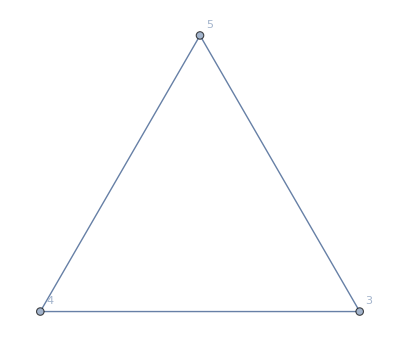
```mathematica
FullSymbol["a",-Graphics-]
```

a345

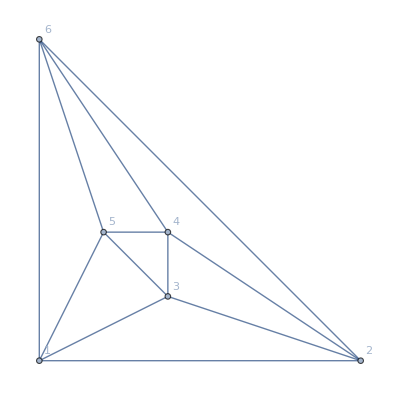

```mathematica
Graph[ReadGrof[4], VertexLabels->"Name",GraphLayout->"PlanarEmbedding"]
```

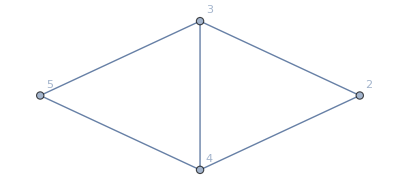

```mathematica
Subgraph[ReadGrof[4],{2,3,4,5}, VertexLabels->"Name"]
```

```mathematica
CalculateInOutFormulaMany[Subgraph[ReadGrof[4],{2,3,4,5}],{{3,4,5},{2}},"a",False]//Simplify
```

a345 (-2+b2)

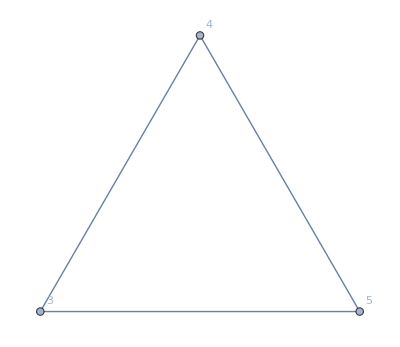
```mathematica
IsomorphicGraphQ[-Graphics-,-Graphics-]
```

True

```mathematica
ChromaticPolynomial[Subgraph[ReadGrof[4],{1,2,3,4,5}],x]//Factor
```

(-2+x) (-1+x) x (7-5 x+x^2)

```mathematica
CalculateInOutFormulaMany[Subgraph[ReadGrof[4],{1,2,3,4,5}],{{3,4,5},{2},{1}},"a",False]//Simplify//Factor
```

a345 (7-3 b2-2 c1+b2 c1)

```mathematica
ChromaticPolynomial[ReadGrof[4],x]//Factor
```

(-2+x) (-1+x) x (-32+29 x-9 x^2+x^3)

```mathematica
(CalculateInOutFormulaMany[Subgraph[ReadGrof[4],{1,2,3,4,5,6}],{{3,4,5},{2},{1},{6}},"a",False]//Simplify//Factor)/.{b2->x,c1->x,d6->x}
```

a345 (-32+29 x-9 x^2+x^3)

```mathematica
Factor[a345 (7+b2 (-3+c1)-2 c1)/.{b2->x,c1->x}]
```

a345 (7-5 x+x^2)

```mathematica
ff=CalculateInOutFormulaMany[Subgraph[ReadGrof[4],{1,2,3,4,5,6}],{{3,4,5},{2},{1},{6}},"a",False]
```

-32 a345+7 a345 b2+7 a345 c1-2 a345 (-b2+b2 c1)+7 a345 d6-2 a345 (-b2+b2 d6)-2 a345 (-c1+c1 d6)+a345 (2 b2-b2 c1-b2 d6+b2 (-c1+c1 d6))

```mathematica
Collect[ff,a345]
```

a345 (-32+9 b2+7 c1-b2 c1-2 (-b2+b2 c1)+7 d6-b2 d6-2 (-b2+b2 d6)-2 (-c1+c1 d6)+b2 (-c1+c1 d6))

```mathematica
ff2=Collect[ff,a345]/a345
```

-32+9 b2+7 c1-b2 c1-2 (-b2+b2 c1)+7 d6-b2 d6-2 (-b2+b2 d6)-2 (-c1+c1 d6)+b2 (-c1+c1 d6)

```mathematica
Collect[ff2,b2]
```

-32+7 c1+7 d6-2 (-c1+c1 d6)+b2 (13-4 c1-3 d6+c1 d6)

```mathematica
Collect[-32+7 c1+7 d6-2 (-c1+c1 d6),c1]
```

-32+c1 (9-2 d6)+7 d6

```mathematica
Factor[-32+c1 (9-2 d6)+7 d6]
```

-32+9 c1+7 d6-2 c1 d6

```mathematica
EdgeList[Graph[ReadGrof[4], VertexLabels->"Name",GraphLayout->"PlanarEmbedding"]]
```

{1<->2,1<->3,1<->5,1<->6,2<->3,2<->4,2<->6,3<->4,3<->5,4<->5,4<->6,5<->6}

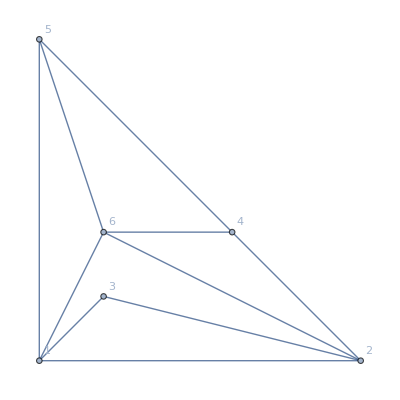

```mathematica
g3=EdgeDelete[Graph[ReadGrof[4], VertexLabels->"Name",GraphLayout->"PlanarEmbedding"],{3<->4,3<->5}]
```

```mathematica
ff3=CalculateInOutFormulaMany[g3,{{1,2,6},{3},{4},{5}},"a",False]
```

-14 a126+7 a126 b3+4 a126 c4-2 a126 b3 c4+4 a126 d5-2 a126 b3 d5-2 a126 (-c4+c4 d5)+a126 b3 (-c4+c4 d5)

```mathematica
Collect[ff3,a126]
```

a126 (-14+7 b3+4 c4-2 b3 c4+4 d5-2 b3 d5-2 (-c4+c4 d5)+b3 (-c4+c4 d5))

```mathematica
Collect[Collect[ff3,a126]/a126,b3]
```

-14+4 c4+4 d5-2 (-c4+c4 d5)+b3 (7-3 c4-2 d5+c4 d5)

```mathematica
Factor[Collect[Collect[ff3,a126]/a126,b3]/.{d5->c4}]
```

(-2+b3) (7-5 c4+c4^2)

```mathematica
Factor[Collect[Collect[ff3,a126]/a126,b3]/.{c4->x,d5->x}]
```

(-2+b3) (7-5 x+x^2)

```mathematica
Factor[(-8+4 b3+4 c4-2 b3 c4+4 d5-2 b3 d5-2 c4 d5+b3 c4 d5)/.{b3->x,c4->x,d5->x}]
```

(-2+x)^3

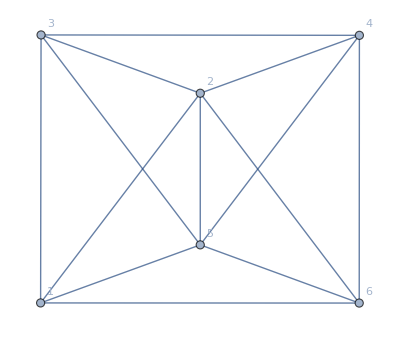

```mathematica
g4=EdgeAdd[g3,{3<->4,3<->5,5<->2}, GraphLayout->"SpringElectricalEmbedding"]
```

```mathematica
ff4=CalculateInOutFormulaMany[g4,{{1,2,6},{3},{4},{5}},"a",False]
```

-39 a126+9 a126 b3+9 a126 c4-3 a126 (-b3+b3 c4)+7 a126 d5-2 a126 (-b3+b3 d5)-2 a126 (-c4+c4 d5)+a126 (2 b3-b3 c4-b3 d5+b3 (-c4+c4 d5))

```mathematica
Collect[ff4,a126]
```

a126 (-39+11 b3+9 c4-b3 c4-3 (-b3+b3 c4)+7 d5-b3 d5-2 (-b3+b3 d5)-2 (-c4+c4 d5)+b3 (-c4+c4 d5))

```mathematica
Collect[-39+11 b3+9 c4-b3 c4-3 (-b3+b3 c4)+7 d5-b3 d5-2 (-b3+b3 d5)-2 (-c4+c4 d5)+b3 (-c4+c4 d5),d5]
```

-39+13 b3+11 c4-2 b3 c4-3 (-b3+b3 c4)+(7-3 b3-2 c4+b3 c4) d5

```mathematica
Collect[-39+11 b3+9 c4-b3 c4-3 (-b3+b3 c4)+7 d5-b3 d5-2 (-b3+b3 d5)-2 (-c4+c4 d5)+b3 (-c4+c4 d5),c4]
```

-39+14 b3+7 d5-b3 d5-2 (-b3+b3 d5)+c4 (11-5 b3-2 d5+b3 d5)

```mathematica
ChromaticPolynomial[g4,x]//Factor
```

(-3+x) (-2+x) (-1+x) x (13-7 x+x^2)

```mathematica
EdgeList[CompleteGraph[5]]
```

{1<->2,1<->3,1<->4,1<->5,2<->3,2<->4,2<->5,3<->4,3<->5,4<->5}

```mathematica
fffc=CalculateInOutFormulaMany[CompleteGraph[5],{{1,2,3},{4},{5}},"a",False]
```

12 a123-3 a123 b4-3 a123 c5+a123 (-b4+b4 c5)

```mathematica
Collect[fffc,a123]
```

a123 (12-4 b4-3 c5+b4 c5)

```mathematica
Collect[Collect[fffc,a123]/a123,b4-3]
```

12-4 b4-3 c5+b4 c5

```mathematica
(a-3)(b-4)//Expand
```

12-4 a-3 b+a b

```mathematica
Factor[fffc]
```

a123 (-3+b4) (-4+c5)

```mathematica
fffc2=CalculateInOutFormulaMany[EdgeDelete[CompleteGraph[5],4<->5],{{1,2,3},{4},{5}},"a",False]
```

9 a123-3 a123 b4-3 a123 c5+a123 b4 c5

```mathematica
Factor[fffc2]
```

a123 (-3+b4) (-3+c5)